# Human_corona, other viruses and vertebrate: Fourier analysis

## Program

```mathematica
nucleotideToComplex[
  DNA_String] := (Characters[
     ToUpperCase[StringReplace[DNA, "\n" -> ""]]] /. {"A" -> 1, "T" -> -1, "G" -> I, "C" -> -I}) /. {_String -> 0};
```

## Corona

```mathematica
seq["corona"]=Import["/BANK/genome/human_corona/Wuhan_corona.fna","Fasta"];
```

```mathematica
sLen["corona"]=((Cpx["corona"]=nucleotideToComplex[seq["corona"][[1]]])//Length)
```

29903

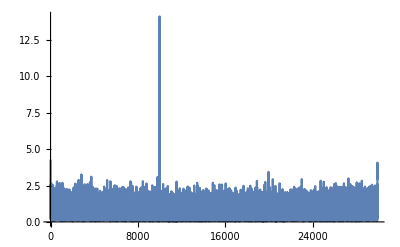

```mathematica
ListPlot[Abs[Fourier[Cpx["corona"]]],Joined->True,PlotRange->All]
```

```mathematica
Position[Abs[Fourier[Cpx["corona"]]],Max[Abs[Fourier[Cpx["corona"]]]]]
```

{{9969}}

```mathematica
sLen["corona"]/(9969-1)//N
```

2.9999

## Window Fourier

```mathematica
tbl[1000]=Table[StringTake[seq["corona"][[1]],{(1000 i)+1,(1000i)+1000}],{i,0,28}];
```

```mathematica
tbl[1000,29]=StringDrop[seq["corona"][[1]],29000];
```

```mathematica
tbl[1000]=Append[tbl[1000],tbl[1000,29]];
```

```mathematica
Cpx[1000]=Map[nucleotideToComplex,tbl[1000]];
```

```mathematica
(CpxF[1000]=Map[Abs[Fourier[#]]&,Cpx[1000]])//Dimensions
```

{30}

```mathematica
CpxFTbl[1000]=Table[{i,CpxF[1000][[j]][[i]]}+{(j-1)*1000,0},{j,1,30},{i,1,1000}];
```

Part::partw: {3.7604,1.66811,2.32228,0.997293,0.532181,1.6885,1.20696,1.8966,«35»,0.385785,0.803473,0.899549,0.702725,0.895686,1.37705,1.24158,«853»}の部分904は存在しません．

Part::partw: {3.7604,1.66811,2.32228,0.997293,0.532181,1.6885,1.20696,1.8966,«35»,0.385785,0.803473,0.899549,0.702725,0.895686,1.37705,1.24158,«853»}の部分905は存在しません．

Part::partw: {3.7604,1.66811,2.32228,0.997293,0.532181,1.6885,1.20696,1.8966,«35»,0.385785,0.803473,0.899549,0.702725,0.895686,1.37705,1.24158,«853»}の部分906は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

```mathematica
CpxFSeq[1000]=Flatten[CpxFTbl[1000],1];
```

```mathematica
CpxFSeqTotal[1000]=Take[CpxFSeq[1000],29903]
```

{{1,1.08167},{2,1.3236},{3,0.243768},{4,0.931946},{5,0.804153},{6,0.626648},29892,{29899,1.75253},{29900,0.14866},{29901,1.38413},{29902,1.14109},{29903,0.509982}}
 |  |  |  |

```mathematica
CpxFSeqTotal[1000]//Length
```

29903

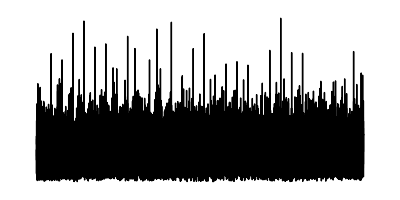

```mathematica
Graphics[FourLine=Line[Map[#*{1,200}+{0,-3800}&,CpxFSeqTotal[1000]]],AspectRatio->1/2]
```

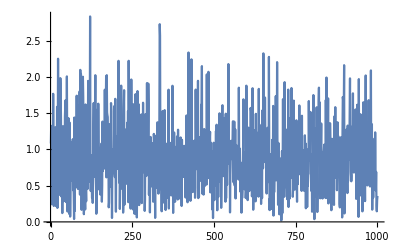
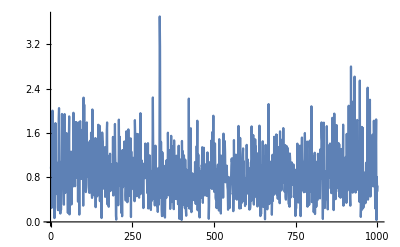
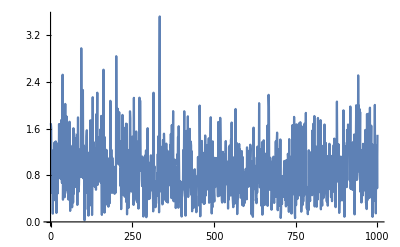
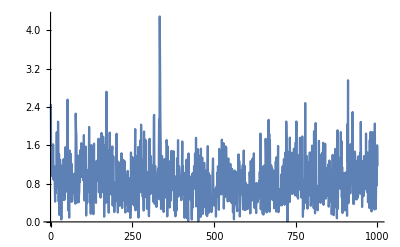
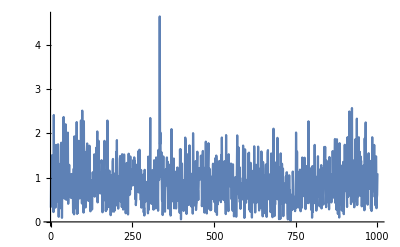
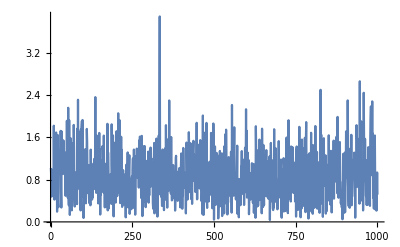
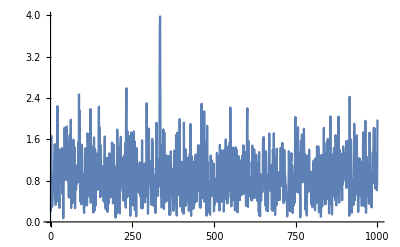
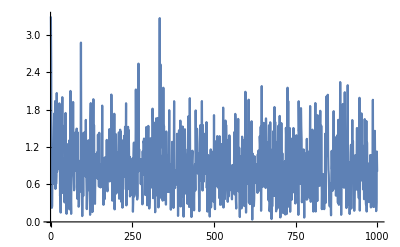

```mathematica
Table[ListPlot[Abs[Fourier[Cpx[1000][[i]]]],Joined->True,PlotRange->All],{i,30}]
```